```mathematica
Practical 1 ( Bisection Method )


Question 1
```

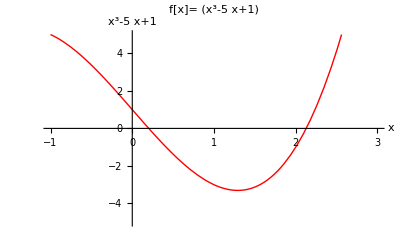

```mathematica
f[x_] := x^3-5*x+1;
Plot[f[x], {x,-1,3}, PlotRange->{-5,5} , 
PlotStyle-> {Red, Thick}, PlotLabel-> "f[x]="f[x],AxesLabel->{x,f[x]}]
```

```mathematica
x0 = 0;
x1 = 1;
Nmax = 20;
eps = 0.0001;
If[N[f[x0]*f[x1]] > 0 ,
Print["Your value do not satisfy the IVP, so change the values"], 
For[i = 1, i≤Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,
Return[N[m]],Print[i,"th iteration value is :", N[m]];
Print["estimated error in" , i , " the iteration is :", N[(x1-x0)/2]];
If[f[m]*f[x1]>0, x1=m, x0=m]]];
Print["Root is: ", m]*
 Print["estimated error in", "the iteration is :", (x1-x0)/2]]
```

1th iteration value is :0.5

estimated error in1 the iteration is :0.5

2th iteration value is :0.25

estimated error in2 the iteration is :0.25

3th iteration value is :0.125

estimated error in3 the iteration is :0.125

4th iteration value is :0.1875

estimated error in4 the iteration is :0.0625

5th iteration value is :0.21875

estimated error in5 the iteration is :0.03125

6th iteration value is :0.203125

estimated error in6 the iteration is :0.015625

7th iteration value is :0.195313

estimated error in7 the iteration is :0.0078125

8th iteration value is :0.199219

estimated error in8 the iteration is :0.00390625

9th iteration value is :0.201172

estimated error in9 the iteration is :0.00195313

10th iteration value is :0.202148

estimated error in10 the iteration is :0.000976563

11th iteration value is :0.20166

estimated error in11 the iteration is :0.000488281

12th iteration value is :0.201416

estimated error in12 the iteration is :0.000244141

13th iteration value is :0.201538

estimated error in13 the iteration is :0.00012207

Return[0.201599]

```mathematica
Question 2
```

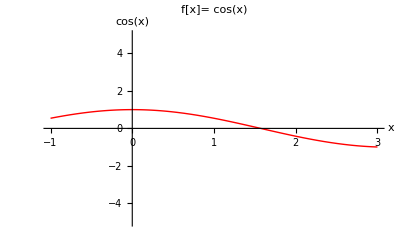

```mathematica
f[x_] := Cos[x];
Plot[f[x], {x, -1, 3}, PlotRange-> {-5,5},
PlotStyle->{Red,Thick}, PlotLabel->"f[x]="f[x], AxesLabel->{x,f[x]}]
```

```mathematica
x0 = 1;
x1=2;
Nmax = 20;
eps = 0.0001;
If[N[f[x0]*f[x1]] > 0,
Print["Your value do not satisfy the IVP, so change the values"],
For[i = 1,i≤ Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2] < eps, 
Return[N[m]], Print[i, "the iteration value is ::", N[m]];
Print["estimated error in", i, "the iteration is:", N[(x1-x0)/2]];
If[f[m]*f[x1]>0, x1=m,x0=m]]];
Print["Root is:",m] *
Print["estimated error in", "the iteration is :",(x1-x0)/2]]
```

1the iteration value is ::1.5

estimated error in1the iteration is:0.5

2the iteration value is ::1.75

estimated error in2the iteration is:0.25

3the iteration value is ::1.625

estimated error in3the iteration is:0.125

4the iteration value is ::1.5625

estimated error in4the iteration is:0.0625

5the iteration value is ::1.59375

estimated error in5the iteration is:0.03125

6the iteration value is ::1.57813

estimated error in6the iteration is:0.015625

7the iteration value is ::1.57031

estimated error in7the iteration is:0.0078125

8the iteration value is ::1.57422

estimated error in8the iteration is:0.00390625

9the iteration value is ::1.57227

estimated error in9the iteration is:0.00195313

10the iteration value is ::1.57129

estimated error in10the iteration is:0.000976563

11the iteration value is ::1.5708

estimated error in11the iteration is:0.000488281

12the iteration value is ::1.57056

estimated error in12the iteration is:0.000244141

13the iteration value is ::1.57068

estimated error in13the iteration is:0.00012207

Return[1.57074]

```mathematica
Question 3
```

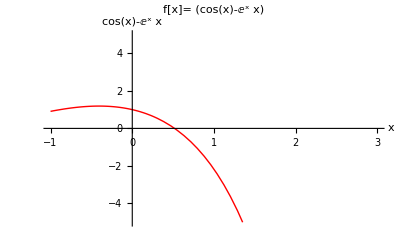

Your value do not satisfy the IVP, so change the values

```mathematica
f[x_]:= Cos[x]-x*Exp[x];
Plot[f[x],{x, -1,3},PlotRange->{-5,5},
PlotStyle-> {Red, Thick}, PlotLabel->"f[x]="f[x],AxesLabel->{x,f[x]}]
```

```mathematica
x0 = 0;
x1 = 1;
Nmax = 20;
eps = 0.0001;
If[N[f[x0]*f[x1]] > 0 ,
Print["Your value do not satisfy the IVP, so change the values"], 
For[i = 1, i≤Nmax, i++, m = (x0+x1)/2;
If[Abs[(x1-x0)/2]<eps,
Return[N[m]],Print[i,"th iteration value is :", N[m]];
Print["estimated error in" , i , " the iteration is :", N[(x1-x0)/2]];
If[f[m]*f[x1]>0, x1=m, x0=m]]];
Print["Root is: ", m]*
 Print["estimated error in", "the iteration is :", (x1-x0)/2]]
```

1th iteration value is :0.5

estimated error in1 the iteration is :0.5

2th iteration value is :0.75

estimated error in2 the iteration is :0.25

3th iteration value is :0.625

estimated error in3 the iteration is :0.125

4th iteration value is :0.5625

estimated error in4 the iteration is :0.0625

5th iteration value is :0.53125

estimated error in5 the iteration is :0.03125

6th iteration value is :0.515625

estimated error in6 the iteration is :0.015625

7th iteration value is :0.523438

estimated error in7 the iteration is :0.0078125

8th iteration value is :0.519531

estimated error in8 the iteration is :0.00390625

9th iteration value is :0.517578

estimated error in9 the iteration is :0.00195313

10th iteration value is :0.518555

estimated error in10 the iteration is :0.000976563

11th iteration value is :0.518066

estimated error in11 the iteration is :0.000488281

12th iteration value is :0.517822

estimated error in12 the iteration is :0.000244141

13th iteration value is :0.5177

estimated error in13 the iteration is :0.00012207

Return[0.517761]